```mathematica
Remove["Global`*"]
expxsqr[y_]:=Integrate[ x^2 y y,{x,-∞,∞},Assumptions->{Re[m ω/h]>0}] 
exppsqr[y_]:=Integrate[y(-h^2 D[y,x,x]),{x,-∞,∞},Assumptions->{Re[m ω/h]>0}]   
ap[y_]:=1/(√(2 m h ω))(m ω x y - h D[y,x]);
am[y_]:=1/(√(2 m h ω))(m ω x y + h D[y,x]);
α=((m ω)/(π h))^(1/4);
ξ=α^2 √π x;
ψo[x_]=α Exp[-ξ^2/2]

ψ1[x_]=ap[ψo[x]]  //PowerExpand//Simplify;
ψ1[x]/ψo[x] //PowerExpand//Simplify
ψ2[x_]=ap[ψ1[x]] //PowerExpand//Simplify;
ψ2[x]/ψo[x] //PowerExpand//Simplify;
p:=Plot[{ψo[x],ψ1[x],ψ2[x]},{x,-5,5}, PlotRange->Full]
expxsqr[ψ1[x]]//PowerExpand//Simplify
exppsqr[ψ1[x]]//PowerExpand//Simplify
```

(ⅇ^(-(m x^2 ω)/(2 h)) ((m ω)/h)^(1/4))/π^(1/4)

(√2 √m x √ω)/(√h)

(3 h)/(2 m ω)

(3 h m ω)/2

```mathematica
16/25 //N
```

0.64

√(2/π) √(1/a)+O[1/a]^(3/2)

(√(2/π) a^(3/2))/k+O[a]^(5/2)

ⅇ^(-a Abs[x])

1-Abs[x] a+O[a]^2

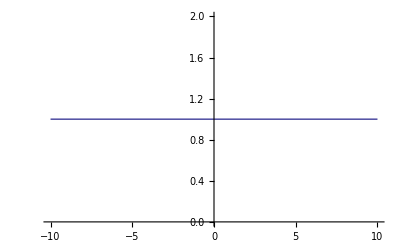

```mathematica
Series[(Sqrt[a/(2 π)]2a)/(k + a^2),{a,∞,1}]
Series[(Sqrt[a/(2 π)]2a)/(k + a^2),{a,0,2}]
Series[Exp[-a Abs[x]],{a,∞,1}]
Series[Exp[-a Abs[x]],{a,0,1}]
Plot[Exp[0Abs[x]],{x,-10,10}]
```